{-2.11947+3291.94 x, | Estimate | Standard Error | t-Statistic | P-Value
1 | -2.11947 | 0.306656 | -6.91155 | 3.50036×10^-6
x | 3291.94 | 117.817 | 27.9411 | 5.24303×10^-15}

{28.5426+0.279006 x, | Estimate | Standard Error | t-Statistic | P-Value
1 | 28.5426 | 3.79184 | 7.52737 | 0.000284807
x | 0.279006 | 0.00942506 | 29.6026 | 9.85242×10^-8}

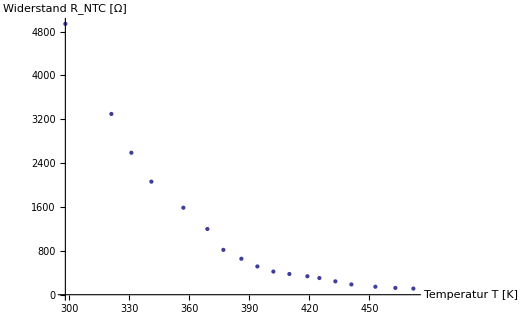

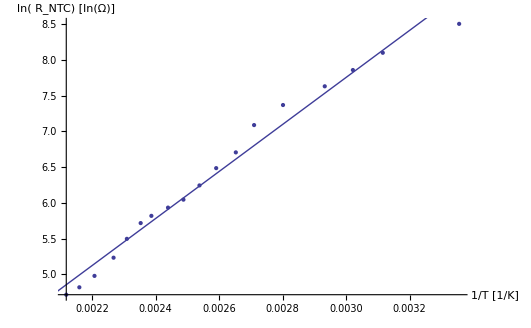

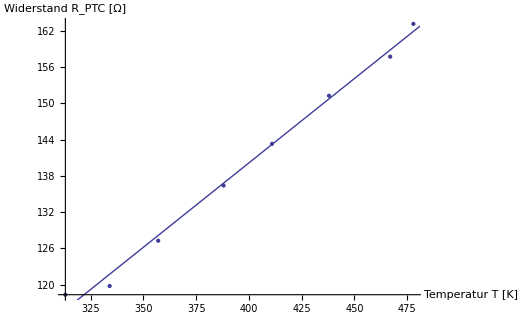

```mathematica
(* Aufgabe 1 *)
widerstand[rPot_,rRef_]:=Module[{},
N[rPot*rRef*1000/(10000-(rPot*1000))]
];
LnBoth[widerstand_]:=Module[{result={}},
For[i=1,i≤Length[widerstand],i++,
AppendTo[result,{N[1/widerstand[[i]][[1]]],N[Log[widerstand[[i]][[2]]]]}] 
];
result
];

Kelvin[t_]:=273+t;

NTC:={{Kelvin[25],widerstand[8.79,680]},
{Kelvin[48],widerstand[8.29,680]},{Kelvin[58],widerstand[7.92,680]}, {Kelvin[68],widerstand[7.52,680]}, {Kelvin[84],widerstand[7,680]}, {Kelvin[96],widerstand[6.38,680]}, {Kelvin[104],widerstand[5.46,680]}, {Kelvin[113],widerstand[4.91,680]}, {Kelvin[121],widerstand[4.31,680]}, {Kelvin[129],widerstand[3.83,680]}, {Kelvin[137],widerstand[3.57,680]}, {Kelvin[146],widerstand[3.31,680]}, {Kelvin[152],widerstand[3.09,680]},{Kelvin[160],widerstand[2.64,680]}, {Kelvin[168],widerstand[2.16,680]},  {Kelvin[180],widerstand[1.76,680]},  {Kelvin[190],widerstand[1.54,680]}, {Kelvin[199],widerstand[1.41,680]} };
NTCLn=LnBoth[NTC];
modelNTC=LinearModelFit[NTCLn,x,x];
modelNTC[{"BestFit","ParameterTable"}]

PTC:={{Kelvin[205],widerstand[6.2,100]},
{Kelvin[194],widerstand[6.12,100]},
{Kelvin[165],widerstand[6.02,100]},
{Kelvin[138],widerstand[5.89,100]},
{Kelvin[115],widerstand[5.77,100]},
{Kelvin[84],widerstand[5.6,100]},
{Kelvin[61],widerstand[5.45,100]},
{Kelvin[40],widerstand[5.42,100]}};

modelPTC=LinearModelFit[PTC,x,x];
modelPTC[{"BestFit","ParameterTable"}]

Show[ListPlot[NTC],AxesLabel->{Style["Temperatur T [K]",12,FontFamily->"Arial"],Style[Row[{"Widerstand ", Subscript["R","NTC"] ," [Ω]"}],12,FontFamily->"Arial"]}]
Show[ListPlot[NTCLn], Plot[modelNTC["BestFit"],{x,0,600}],AxesLabel->{Style["1/T [1/K]",12,FontFamily->"Arial"],Style[Row[{"ln( ", Subscript["R","NTC"] ,") [ln(Ω)]"}]]}]

Show[ListPlot[PTC], Plot[modelPTC["BestFit"],{x,0,600}],AxesLabel->{Style["Temperatur T [K]",12,FontFamily->"Arial"],Style[Row[{"Widerstand ", Subscript["R","PTC"] ," [Ω]"}],12,FontFamily->"Arial"]}]
```

{{297,0.0238095},{289,0.0228571},{284,0.0225397},{279,0.0222222},{274,0.021873},{269,0.0215238},{264,0.0180159},{259,0.020873},{254,0.0205556},{249,0.020254},{244,0.0199206},{239,0.019619},{234,0.0192857},{229,0.0189683},{224,0.0186508},{219,0.0183016},{215,0.0180159},{210,0.0177143},{205,0.0173651},{200,0.0170159},{195,0.0166667},{190,0.0163175},{185,0.0158254},{180,0.0120794},{175,0.00987302},{170,0.00873016}}

{{165,0.0146825},{160,0.0139683},{155,0.00653968},{150,0.000349206},{145,0.000301587},{140,0.000285714},{135,0.000206349},{130,0.000142857},{125,0.0000634921},{120,0.},{115,0.000047619}}

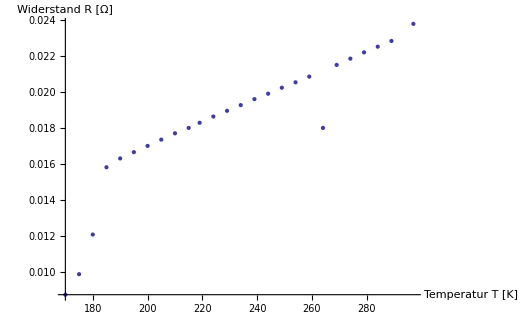

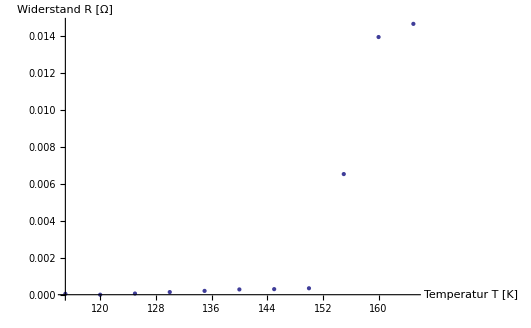

```mathematica
(* Aufgabe 5 *)
widerstand1[u_]:=N[u/63];
werte1:={{Kelvin[24],widerstand1[1.5]},{Kelvin[16],widerstand1[1.44]},
{Kelvin[11],widerstand1[1.42]},
{Kelvin[6],widerstand1[1.4]},
{Kelvin[1],widerstand1[1.378]},
{Kelvin[-4],widerstand1[1.356]},
{Kelvin[-9],widerstand1[1.135]},
{Kelvin[-14],widerstand1[1.315]},
{Kelvin[-19],widerstand1[1.295]},
{Kelvin[-24],widerstand1[1.276]},
{Kelvin[-29],widerstand1[1.255]},
{Kelvin[-34],widerstand1[1.236]},
{Kelvin[-39],widerstand1[1.215]},
{Kelvin[-44],widerstand1[1.195]},
{Kelvin[-49],widerstand1[1.175]},
{Kelvin[-54],widerstand1[1.153]},
{Kelvin[-58],widerstand1[1.135]},
{Kelvin[-63],widerstand1[1.116]},
{Kelvin[-68],widerstand1[1.094]},
{Kelvin[-73],widerstand1[1.072]},
{Kelvin[-78],widerstand1[1.05]},
{Kelvin[-83],widerstand1[1.028]},
{Kelvin[-88],widerstand1[0.997]},
{Kelvin[-93],widerstand1[0.761]},
{Kelvin[-98],widerstand1[0.622]},
{Kelvin[-103],widerstand1[0.55]}};

werte2:={{Kelvin[-108],widerstand1[0.925]},
{Kelvin[-113],widerstand1[0.880]},
{Kelvin[-118],widerstand1[0.412]},
{Kelvin[-123],widerstand1[0.022]},
{Kelvin[-128],widerstand1[0.019]},
{Kelvin[-133],widerstand1[0.018]},
{Kelvin[-138],widerstand1[0.013]},
{Kelvin[-143],widerstand1[0.009]},
{Kelvin[-148],widerstand1[0.004]},
{Kelvin[-153],widerstand1[0]},
{Kelvin[-158],widerstand1[0.003]}};

werte1
werte2

Show[ListPlot[werte1],AxesLabel->{Style["Temperatur T [K]",12,FontFamily->"Arial"],Style["Widerstand R [Ω]"],12,FontFamily->"Arial"}]
Show[ListPlot[werte2],AxesLabel->{Style["Temperatur T [K]",12,FontFamily->"Arial"],Style["Widerstand R [Ω]"],12,FontFamily->"Arial"}]
```